## Problem 1 (b)

```mathematica
minus = {1/(√2), -1/(√2)};ρ0= ArrayFlatten[Outer[Times,minus,minus]]; MatrixForm[ρ0]
```

(1/2 | -1/2
-1/2 | 1/2)

```mathematica
ham1 = {{-1/2*ℏ*ω0, 0},{0,1/2*ℏ*ω0}};MatrixForm[ham1]
```

(-(ω0 ℏ)/2 | 0
0 | (ω0 ℏ)/2)

```mathematica
U = MatrixExp[-I*t/ℏ*ham1];MatrixForm[U]
```

(ⅇ^((ⅈ t ω0)/2) | 0
0 | ⅇ^(-1/2 ⅈ t ω0))

```mathematica
Udagger = MatrixExp[I*t/ℏ*ham1];MatrixForm[Udagger]
```

(ⅇ^(-1/2 ⅈ t ω0) | 0
0 | ⅇ^((ⅈ t ω0)/2))

```mathematica
ρt = U.ρ0.Udagger; MatrixForm[ρt]
```

(1/2 | -1/2 ⅇ^(ⅈ t ω0)
-1/2 ⅇ^(-ⅈ t ω0) | 1/2)

```mathematica
pauliy = {{0,-I},{I,0}}; MatrixForm[pauliy]
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
expectation = FullSimplify[Tr[ρt.pauliy]]
```

Sin[t ω0]

## Problems 1 (d) and 1(e)

```mathematica
psiminus = {0,1/(√2), -1/(√2),0};op1= ArrayFlatten[Outer[Times,psiminus,psiminus]]; MatrixForm[op1]
```

(0 | 0 | 0 | 0
0 | 1/2 | -1/2 | 0
0 | -1/2 | 1/2 | 0
0 | 0 | 0 | 0)

```mathematica
eyet2 =  ArrayFlatten[TensorProduct[IdentityMatrix[2],IdentityMatrix[2],1]]; MatrixForm[eyet2]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
ρw = (p)*op1 + eyet2*(1-p)/4; MatrixForm[ρw]
```

((1-p)/4 | 0 | 0 | 0
0 | (1-p)/4+p/2 | -p/2 | 0
0 | -p/2 | (1-p)/4+p/2 | 0
0 | 0 | 0 | (1-p)/4)

```mathematica
Tr[ρw]
```

1

```mathematica
purity = FullSimplify[Tr[ρw.ρw]]
```

1/4 (1+3 p^2)

## Problem 2(a)

```mathematica
sz = {{1,0}, {0, -1}}; MatrixForm[sz]
```

(1 | 0
0 | -1)

```mathematica
si = IdentityMatrix[2]; MatrixForm[si]
```

(1 | 0
0 | 1)

```mathematica
sza = ArrayFlatten[TensorProduct[sz,si]]; MatrixForm[sza]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
szb = ArrayFlatten[TensorProduct[si,sz]]; MatrixForm[szb]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
Umat = MatrixExp[-I*t/2*(ωa*sza + ωb*szb)]; MatrixForm[Umat]
```

(ⅇ^(-1/2 ⅈ t (ωa+ωb)) | 0 | 0 | 0
0 | ⅇ^(-1/2 ⅈ t (ωa-ωb)) | 0 | 0
0 | 0 | ⅇ^(1/2 ⅈ t (ωa-ωb)) | 0
0 | 0 | 0 | ⅇ^(1/2 ⅈ t (ωa+ωb)))

```mathematica
Umatdot = D[Umat,t]; MatrixForm[Umatdot]
```

(-1/2 ⅈ ⅇ^(-1/2 ⅈ t (ωa+ωb)) (ωa+ωb) | 0 | 0 | 0
0 | -1/2 ⅈ ⅇ^(-1/2 ⅈ t (ωa-ωb)) (ωa-ωb) | 0 | 0
0 | 0 | 1/2 ⅈ ⅇ^(1/2 ⅈ t (ωa-ωb)) (ωa-ωb) | 0
0 | 0 | 0 | 1/2 ⅈ ⅇ^(1/2 ⅈ t (ωa+ωb)) (ωa+ωb))

```mathematica
HLab = -1/2*ℏ*ωa*sza + -1/2*ℏ*ωb*szb + ℏ*g*(sza.szb); MatrixForm[HLab]
```

(g ℏ-(ωa ℏ)/2-(ωb ℏ)/2 | 0 | 0 | 0
0 | -g ℏ-(ωa ℏ)/2+(ωb ℏ)/2 | 0 | 0
0 | 0 | -g ℏ+(ωa ℏ)/2-(ωb ℏ)/2 | 0
0 | 0 | 0 | g ℏ+(ωa ℏ)/2+(ωb ℏ)/2)

```mathematica
HRot = FullSimplify[Umat.HLab.ConjugateTranspose[Umat] + I*ℏ*Umatdot.ConjugateTranspose[Umat], Assumptions->{t∈Reals && ωa∈Reals && ωb∈Reals}];
MatrixForm[HRot]
```

(g ℏ | 0 | 0 | 0
0 | -g ℏ | 0 | 0
0 | 0 | -g ℏ | 0
0 | 0 | 0 | g ℏ)

```mathematica
MatrixForm[ℏ*g*sza.szb]
```

(g ℏ | 0 | 0 | 0
0 | -g ℏ | 0 | 0
0 | 0 | -g ℏ | 0
0 | 0 | 0 | g ℏ)

## Problem 2(b)

```mathematica
Uzz = MatrixExp[-I*t/ℏ*HRot]; MatrixForm[Uzz]
```

(ⅇ^(-ⅈ g t) | 0 | 0 | 0
0 | ⅇ^(ⅈ g t) | 0 | 0
0 | 0 | ⅇ^(ⅈ g t) | 0
0 | 0 | 0 | ⅇ^(-ⅈ g t))

## Problem 2(c)

```mathematica
Rz = {{Exp[-I/2*(-π/2)],0},{0,Exp[I/2*(-π/2)]}};MatrixForm[Rz]
```

(ⅇ^((ⅈ π)/4) | 0
0 | ⅇ^(-(ⅈ π)/4))

```mathematica
Rza = ArrayFlatten[TensorProduct[Rz,si]]; MatrixForm[Rza]
```

(ⅇ^((ⅈ π)/4) | 0 | 0 | 0
0 | ⅇ^((ⅈ π)/4) | 0 | 0
0 | 0 | ⅇ^(-(ⅈ π)/4) | 0
0 | 0 | 0 | ⅇ^(-(ⅈ π)/4))

```mathematica
Rzb = ArrayFlatten[TensorProduct[si,Rz]]; MatrixForm[Rzb]
```

(ⅇ^((ⅈ π)/4) | 0 | 0 | 0
0 | ⅇ^(-(ⅈ π)/4) | 0 | 0
0 | 0 | ⅇ^((ⅈ π)/4) | 0
0 | 0 | 0 | ⅇ^(-(ⅈ π)/4))

```mathematica
CZtgate[t_] =  Exp[-I*π/4]*(Rza.Rzb.Uzz); MatrixForm[CZtgate[t]]
```

(ⅈ ⅇ^(-(ⅈ π)/4-ⅈ g t) | 0 | 0 | 0
0 | ⅇ^(-(ⅈ π)/4+ⅈ g t) | 0 | 0
0 | 0 | ⅇ^(-(ⅈ π)/4+ⅈ g t) | 0
0 | 0 | 0 | -ⅈ ⅇ^(-(ⅈ π)/4-ⅈ g t))

```mathematica
CZ = {{1, 0, 0,0},{0, 1, 0,0},{0, 0, 1,0},{0, 0, 0,-1}}; MatrixForm[CZ]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
Solve[CZtgate[tgate] == CZ, {tgate}]
```

{{tgate→ConditionalExpression[(ⅈ (-(ⅈ π)/4+2 ⅈ π C[1]))/g, C[1]∈ℤ]}}

```mathematica
tgate =FullSimplify[ (ⅈ (-(ⅈ π)/4))/g]
```

π/(4 g)

## Problem 2(f)

```mathematica
plus = {1/(√2), 1/(√2)}; minus = {1/(√2), -1/(√2)};
```

```mathematica
plusminus = ArrayFlatten[TensorProduct[plus,minus],1]; MatrixForm[plusminus]
```

(1/2
-1/2
1/2
-1/2)

```mathematica
ρab = ArrayFlatten[Outer[Times,plusminus,plusminus]]; MatrixForm[ρab]
```

(1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4
1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4)

```mathematica
ρabt = FullSimplify[Uzz.ρab.ConjugateTranspose[Uzz], Assumptions->{t∈Reals && g∈Reals}];MatrixForm[ρabt]
```

(1/4 | -1/4 ⅇ^(-2 ⅈ g t) | 1/4 ⅇ^(-2 ⅈ g t) | -1/4
-1/4 ⅇ^(2 ⅈ g t) | 1/4 | -1/4 | 1/4 ⅇ^(2 ⅈ g t)
1/4 ⅇ^(2 ⅈ g t) | -1/4 | 1/4 | -1/4 ⅇ^(2 ⅈ g t)
-1/4 | 1/4 ⅇ^(-2 ⅈ g t) | -1/4 ⅇ^(-2 ⅈ g t) | 1/4)

```mathematica
partialTrρabt =FullSimplify[{{ρabt[[1,1]]+ρabt[[2,2]],ρabt[[1,3]]+ρabt[[2,4]]},{ρabt[[3,1]]+ρabt[[4,2]],ρabt[[3,3]]+ρabt[[4,4]]}}]; MatrixForm[partialTrρabt]
```

(1/2 | 1/2 Cos[2 g t]
1/2 Cos[2 g t] | 1/2)

```mathematica
statepurity = FullSimplify[Tr[partialTrρabt.partialTrρabt]]
```

1/4 (3+Cos[4 g t])

```mathematica
stateconcurrence =FullSimplify[ √(2*(1-Tr[partialTrρabt.partialTrρabt]))]
```

√(Sin[2 g t]^2)

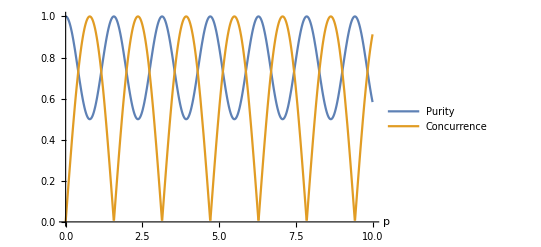

```mathematica
g = 1;
p1 = Plot[{statepurity,stateconcurrence}, {t, 0, 10}, PlotRange->All, PlotLegends->{"Purity","Concurrence"}, AxesLabel->{"p",""}]
```

## Problem 2(g)

```mathematica
Clear[k,g, t]
Series[1/2 Cos[2*k], {k, 0, 2}]
```

1/2-k^2+O[k]^3

```mathematica
Series[1/2*ⅇ^(-(t/T2)^2), {t, 0, 2}]
```

1/2-t^2/(2 T2^2)+O[t]^3

```mathematica
Solve[1/2-t^2/(2 T2^2)==1/2-k^2, {T2}]
```

{{T2→-t/(√2 k)},{T2→t/(√2 k)}}

```mathematica
FullSimplify[t/(√2 k), Assumptions->{k = g*t}]
```

1/(√2 g)